```mathematica
Solve[(C-c)/t==q-(k *((C-c)/2)), C]
```

{{C→(2 c+c k t+2 q t)/(2+k t)}}

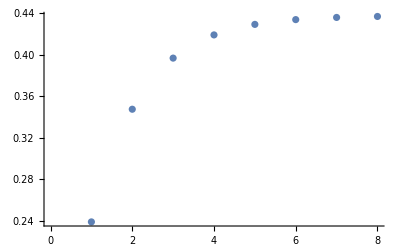

```mathematica
num=ListPlot[{0.23913826245327652,
0.34765071442625767,
0.3968898119775714,
0.4192327660218821,
0.4293712051942479,
0.433971668886198,
0.43605919595236003,
0.43700644160926727}]
```

```mathematica
c= (Co-q/k) Exp[-k t] +q/k
```

q/k+ⅇ^(-k t) (Co-q/k)

```mathematica
cval = c /. {q->(14716*.000022354),k-> .7515, Co->0}
```

0.43774-0.43774 ⅇ^(-0.7515 t)

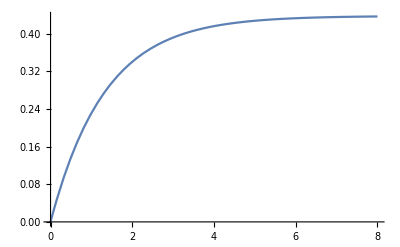

```mathematica
ana=Plot[cval,{t,0,8}]
```

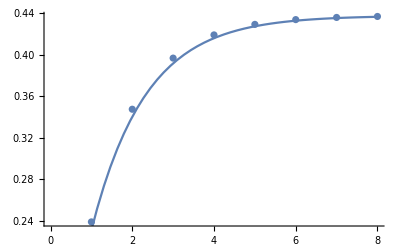

```mathematica
Show[{num,ana}]
```

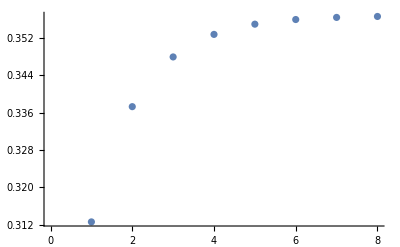

```mathematica
ListPlot[{0.31260610041849946,
0.337252432292013,
0.3478841173469304,
0.35270579922994,
0.3548936950152265,
0.3558864843752476,
0.3563369769337302,
0.3565413944602888}]
```

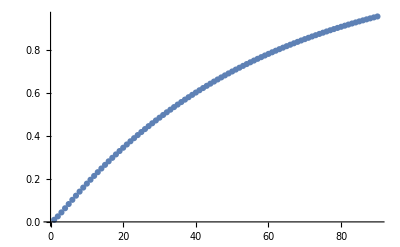

```mathematica
ListPlot[{0.009849885883875031,0.025746250538637765,0.04418473206163544,0.06357873082755837,0.08321179692103073,0.102762261859279,0.12208753443437963,0.14112622289342452,0.15985372250812363,0.1782620638211401,0.19635076950788571,0.2141227065392568,0.23158220501702287,0.2487342055275506,0.26558387318370336,0.2821364234166383,0.29839704383585625,0.31437085966556916,0.3300629189386934,0.3454781866406686,0.3606215428991805,0.3754977829948296,0.3901116181834029,0.40446767687200336,0.4185705059415831,0.4324245721219947,0.44603426337720353,0.45940389028168405,0.472537687379623,0.4854398145233634,0.4981143581896984,0.510565332773609,0.5227966818594815,0.5348122794700374,0.5466159312932966,0.5582113758879244,0.5696022858673305,0.5807922690628876,0.5917848696666334,0.6025835693538178,0.6131917883856511,0.6236128866925982,0.6338501649385664,0.6439068655663217,0.653786173824464,0.6634912187762878,0.6730250742908468,0.6823907600165381,0.6915912423375117,0.7006294353132108,0.7095082016013384,0.7182303533645449,0.7267986531611204,0.7352158148199776,0.7434845043002,0.7516073405354284,0.7595868962633531,0.7674256988405745,0.7751262310430904,0.7826909318526626,0.7901221972293135,0.7974223808701962,0.8045937949550783,0.8116387108786766,0.8185593599700731,0.8253579341994424,0.8320365868723114,0.838597433311574,0.8450425515274752,0.8513739828757769,0.8575937327043148,0.86370377098815,0.869706032953517,0.8756024196907664,0.8813947987564947,0.8870850047650546,0.8926748399696294,0.8981660748330595,0.9035604485885994,0.9088596697907827,0.9140654168565714,0.9191793385969589,0.9242030547391962,0.9291381564398069,0.9339862067885522,0.9387487413035066,0.9434272684174014,0.948023269955389,0.9525382016043794,0.9569734933740992,}]
```